```mathematica
RotationMatrix[θ].{{α,β},{γ,δ}}.RotationMatrix[-θ]//FullSimplify
Eigenvalues[{{α,β},{γ,δ}}]//FullSimplify
Eigenvalues[RotationMatrix[θ].{{α,β},{γ,δ}}.RotationMatrix[-θ]]//FullSimplify
```

{{α Cos[θ]^2-(β+γ) Cos[θ] Sin[θ]+δ Sin[θ]^2,β Cos[θ]^2+(α-δ) Cos[θ] Sin[θ]-γ Sin[θ]^2},{γ Cos[θ]^2+(α-δ) Cos[θ] Sin[θ]-β Sin[θ]^2,δ Cos[θ]^2+(β+γ) Cos[θ] Sin[θ]+α Sin[θ]^2}}

{1/2 (α-√(4 β γ+(α-δ)^2)+δ),1/2 (α+√(4 β γ+(α-δ)^2)+δ)}

{1/2 (α-√(4 β γ+(α-δ)^2)+δ),1/2 (α+√(4 β γ+(α-δ)^2)+δ)}

```mathematica
(m=Table[Π[μ][ν],{μ,{τ,x,y,H}},{ν,{τ,x,y,H}}]/.{Π[H][τ]->0,Π[H][x]->0,Π[H][y]->0,Π[τ][H]->0,Π[x][H]->0,Π[y][H]->0})//MatrixForm
```

(Π[τ][τ] | Π[τ][x] | Π[τ][y] | 0
Π[x][τ] | Π[x][x] | Π[x][y] | 0
Π[y][τ] | Π[y][x] | Π[y][y] | 0
0 | 0 | 0 | Π[H][H])

```mathematica
(Λ=FullSimplify[D[{τ,√(x^2+y^2),ArcTan[x,y],H},{{τ,x,y,H}}]/.{x->r Cos[ϕ],y->r Sin[ϕ]},r>0])//MatrixForm
Λ.m.Transpose[Λ]/.{Sinh[H]->0,Cosh[H]->1}//FullSimplify//MatrixForm
%/.{Π->Π̃,Π[H][H]->(Π̃[H][H])/τ^2,Sinh[H]->0,Cosh[H]->1}//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[ϕ] | Sin[ϕ] | 0
0 | -Sin[ϕ]/r | Cos[ϕ]/r | 0
0 | 0 | 0 | 1)

(Π[τ][τ] | Cos[ϕ] Π[τ][x]+Sin[ϕ] Π[τ][y] | (-Sin[ϕ] Π[τ][x]+Cos[ϕ] Π[τ][y])/r | 0
Cos[ϕ] Π[x][τ]+Sin[ϕ] Π[y][τ] | Cos[ϕ]^2 Π[x][x]+Sin[ϕ] (Cos[ϕ] (Π[x][y]+Π[y][x])+Sin[ϕ] Π[y][y]) | (-Cos[ϕ] Sin[ϕ] Π[x][x]+Cos[ϕ]^2 Π[x][y]+Sin[ϕ] (-Sin[ϕ] Π[y][x]+Cos[ϕ] Π[y][y]))/r | 0
(-Sin[ϕ] Π[x][τ]+Cos[ϕ] Π[y][τ])/r | (-Cos[ϕ] Sin[ϕ] Π[x][x]-Sin[ϕ]^2 Π[x][y]+Cos[ϕ] (Cos[ϕ] Π[y][x]+Sin[ϕ] Π[y][y]))/r | (Sin[ϕ]^2 Π[x][x]+Cos[ϕ] (-Sin[ϕ] (Π[x][y]+Π[y][x])+Cos[ϕ] Π[y][y]))/r^2 | 0
0 | 0 | 0 | Π[H][H])

(Π̃[τ][τ] | Cos[ϕ] Π̃[τ][x]+Sin[ϕ] Π̃[τ][y] | (-Sin[ϕ] Π̃[τ][x]+Cos[ϕ] Π̃[τ][y])/r | 0
Cos[ϕ] Π̃[x][τ]+Sin[ϕ] Π̃[y][τ] | Cos[ϕ]^2 Π̃[x][x]+Sin[ϕ] (Cos[ϕ] (Π̃[x][y]+Π̃[y][x])+Sin[ϕ] Π̃[y][y]) | (-Cos[ϕ] Sin[ϕ] Π̃[x][x]+Cos[ϕ]^2 Π̃[x][y]+Sin[ϕ] (-Sin[ϕ] Π̃[y][x]+Cos[ϕ] Π̃[y][y]))/r | 0
(-Sin[ϕ] Π̃[x][τ]+Cos[ϕ] Π̃[y][τ])/r | (-Cos[ϕ] Sin[ϕ] Π̃[x][x]-Sin[ϕ]^2 Π̃[x][y]+Cos[ϕ] (Cos[ϕ] Π̃[y][x]+Sin[ϕ] Π̃[y][y]))/r | (Sin[ϕ]^2 Π̃[x][x]+Cos[ϕ] (-Sin[ϕ] (Π̃[x][y]+Π̃[y][x])+Cos[ϕ] Π̃[y][y]))/r^2 | 0
0 | 0 | 0 | (Π̃[H][H])/τ^2)

```mathematica
(Λ=FullSimplify[D[{τ Cosh[H],x,y,τ Sinh[H]},{{τ,x,y,H}}]])//MatrixForm
Print["At mid-rapidity (H==0):"];
(Table[Π[μ][ν],{μ,{t,x,y,z}},{ν,{t,x,y,z}}]//MatrixForm)==((Λ.m.Transpose[Λ]/.{Sinh[H]->0,Cosh[H]->1}//FullSimplify)//MatrixForm)
(Table[Π[μ][ν],{μ,{t,x,y,z}},{ν,{t,x,y,z}}]//MatrixForm)==((Λ.m.Transpose[Λ]/.{Π->Π̃,Π[H][H]->(Π̃[H][H])/τ^2,Sinh[H]->0,Cosh[H]->1}//FullSimplify)//MatrixForm)
```

(Cosh[H] | 0 | 0 | τ Sinh[H]
0 | 1 | 0 | 0
0 | 0 | 1 | 0
Sinh[H] | 0 | 0 | τ Cosh[H])

At mid-rapidity (H==0):

(Π[t][t] | Π[t][x] | Π[t][y] | Π[t][z]
Π[x][t] | Π[x][x] | Π[x][y] | Π[x][z]
Π[y][t] | Π[y][x] | Π[y][y] | Π[y][z]
Π[z][t] | Π[z][x] | Π[z][y] | Π[z][z])==(Π[τ][τ] | Π[τ][x] | Π[τ][y] | 0
Π[x][τ] | Π[x][x] | Π[x][y] | 0
Π[y][τ] | Π[y][x] | Π[y][y] | 0
0 | 0 | 0 | τ^2 Π[H][H])

(Π[t][t] | Π[t][x] | Π[t][y] | Π[t][z]
Π[x][t] | Π[x][x] | Π[x][y] | Π[x][z]
Π[y][t] | Π[y][x] | Π[y][y] | Π[y][z]
Π[z][t] | Π[z][x] | Π[z][y] | Π[z][z])==(Π̃[τ][τ] | Π̃[τ][x] | Π̃[τ][y] | 0
Π̃[x][τ] | Π̃[x][x] | Π̃[x][y] | 0
Π̃[y][τ] | Π̃[y][x] | Π̃[y][y] | 0
0 | 0 | 0 | Π̃[H][H])

```mathematica
(*Double check that necessary and sufficient conditions are being evaluated correctly*)
Remove["Global`*"];
ClearAll["Global`*"];
```

```mathematica
(*πμν=({{-π00,-π01,-π02,-π03},
{π10,π11,π12,π13},
{π20,π21,π22,π23},
{π30,π31,π32,π33}}//.({π10->π01,π20->π02,π21->π12,π31->0,π13->0,π30->0,π03->0,π32->0,π23->0,π00->Rationalize[#1,0],π01->Rationalize[#2,0],π02->Rationalize[#3,0],π11->Rationalize[#4,0],π12->Rationalize[#5,0],π22->Rationalize[#6,0],π33->Rationalize[#7,0]}&[0.1469770080856057,-0.04772652758077559,-0.2873961914626526,0.4091716349588435,0.03723144471444706,0.5349437112349582,-4.98211461317622 0.4^2]));*)
πμν=({{-π00,-π01,-π02,-π03},
{π10,π11,π12,π13},
{π20,π21,π22,π23},
{π30,π31,π32,π33}}//.({π10->π01,π20->π02,π21->π12,π30->π03,π31->π13,π32->π23,π00->Rationalize[#1,0],π01->Rationalize[#2,0],π02->Rationalize[#3,0],π03->Rationalize[#4,0],π11->Rationalize[#5,0],π12->Rationalize[#6,0],π13->Rationalize[#7,0],π22->Rationalize[#8,0],π23->Rationalize[#9,0],π33->Rationalize[#10,0]}&[0.00092957306846696,-0.0153368068256983,-0.0172574092075577,-0.199041019722235,0.268491808630193,0.0131314914398429,0.449567949133594,0.0722138992178898,0.347518553369308,-0.339776134779616]));
(*check1: 3.5078 10^-7,0.0013504,-0.0045209,0.21482,0.00048869,0.2144,-0.42917*)
(*check2: 0.37987993 10^-4,0.26556597 10^-1,0.55875212 10^-2,20.007846,-0.79495762,16.140470,-36.148278*)
(*check3: 0.0101183,-0.00934934,-0.0294361,0.0669258,0.00231139,0.0779106,-0.134718*)
(*check4: -0.0184099,-0.0351468,-0.0226025,0.0559556,-0.0290008,-0.0439037,-0.0304617*)
(*check5: 0.273139,-0.171069,0.337599,-0.0284401,-0.198412,0.396063,-0.0944836*)
(*check6a: 0.03888654545,0.06286225437,-0.1394259743,0.05630938684,-0.1361104489,0.4004696945,-0.4178925359*)
(*check6b: 0.0410670291827368,0.06458252754198099,-0.1432414716332558, 0.05630938684102632,-0.1361104488951961,0.4004696944887345,-2.598200325918905 0.4^2*)
(*check6c: 0.1095139205549313,-0.05557358014063064,-0.2355731009321679,0.06580270373413311,0.1664968810120401,0.4721349779266837,-2.677648506911781 0.4^2*)
(*check6d: 0.00390748020123648,0.04189702736261648,-0.03035663092013481,0.06202294012874295,-0.1142594686104363,0.1495667522329585,-1.298013826002907 0.4^2*)
(*check6e: 0.1215879096367744,0.01053910132382408,-0.2282305798282588,0.1014836275122843,-0.04232458750359964,0.4192206263349442,-2.494477151315337 0.4^2*)
(*check7a: 0.1469770080856057,-0.04772652758077559,-0.2873961914626526,0.4091716349588435,0.03723144471444706,0.5349437112349582,-4.98211461317622 0.4^2*)
(*check7b: 0.1399727962,-0.04658592028,-0.2805277639,0.409171635,0.03723144471,0.5349437112,-0.80414255*)
rands={0.74865109357051551342010498046875`10.,0.7832718014833517372608184814453125`10.,0.6676001377054490149021148681640625`10.,0.6540939719998277723789215087890625`10.,0.1373497792519629001617431640625`10.,
0.148469168343581259250640869140625`10.,0.9348005827632732689380645751953125`10.,0.707913367426954209804534912109375`10.,0.9495418449514545500278472900390625`10.,0.3749321712530218064785003662109375`10.,0.4646400814526714384555816650390625`10.,0.8826349160517565906047821044921875`10.,0.6741853063576854765415191650390625`10.}
rules1={Λ1->#[[1]],Λ2->#[[2]],Λ3->#[[3]]}&[SortBy[N[Eigenvalues[πμν],10],Abs][[2;;]]//Sort];
rules2=MapThread[(#1->#2)&,{{e,p,Π,τπ,τΠ,η,ζ,τππ,δΠΠ,λΠπ,δππ,λπΠ,cs2},rands}];
rules=rules1~Join~rules2
{#[[1]],#[[2]]/(√Abs[(#[[2,1]])^2-(#[[2,2]])^2-(#[[2,3]])^2-(#[[2,4]])^2])}&/@(N[Eigensystem[πμν],10]//Transpose)//MatrixForm
(*{Λ1->-0.42917,Λ2->0.21417257864400185,Λ3->0.21515131908706256,e->0.8359781978670136,p->0.8914120229818119,Π->0.6494736842218722,τπ->0.9779736841861808,τΠ->0.7560163379095179,η->0.20396169274741482,ζ->0.7762122851374313,τππ->0.040580307715428754,δΠΠ->0.7635349988563378,λΠπ->0.650383154425864,δππ->0.6567957390430446,λπΠ->0.1682514706808378,cs2->0.30578929353297357}*)
```

{0.7486510936,0.7832718015,0.6676001377,0.654093972,0.1373497793,0.1484691683,0.9348005828,0.7079133674,0.949541845,0.3749321713,0.4646400815,0.8826349161,0.6741853064}

{Λ1→-0.6638603038,Λ2→0.1111466074,Λ3→0.5527136964,e→0.7486510936,p→0.7832718015,Π→0.6676001377,τπ→0.654093972,τΠ→0.1373497793,η→0.1484691683,ζ→0.9348005828,τππ→0.7079133674,δΠΠ→0.949541845,λΠπ→0.3749321713,δππ→0.4646400815,λπΠ→0.8826349161,cs2→0.6741853064}

(-0.6638603038 | {-0.236159214,-0.409480087,-0.400891338,0.852867732}
0.5527136964 | {0.215670107,0.804668412,0.379478296,0.504993628}
0.1111466074 | {0.331920278,-0.444158039,0.945266046,0.139164681}
-9.414769487×10^-18 | {-1.10111573,-0.111541734,-0.44524773,0.0420564002})

```mathematica
πμν//Tr//N
```

-1.44323×10^-16

```mathematica
{(#[[2,1]])^2-(#[[2,2]])^2-(#[[2,3]])^2-(#[[2,4]])^2}&/@(%)//MatrixForm
```

(-1.
-1.
1.
-1.)

```mathematica
necessaryConditionsLHS={
(2η+λπΠ Π)-1/2 τππ Abs[Λ1],
e+p+Π-1/(2τπ)(2η+λπΠ Π)-τππ/(4τπ)Λ3,
1/(2τπ)(2η+λπΠ Π)+τππ/(4τπ)(Λ1+Λ2),
1/(2τπ)(2η+λπΠ Π)+τππ/(4τπ)(Λ1+Λ3),
1/(2τπ)(2η+λπΠ Π)+τππ/(4τπ)(Λ3+Λ2),
e+p+Π+Λ1-1/(2τπ)(2η+λπΠ Π)-τππ/(4τπ)(Λ1+Λ2),
e+p+Π+Λ1-1/(2τπ)(2η+λπΠ Π)-τππ/(4τπ)(Λ1+Λ3),
e+p+Π+Λ2-1/(2τπ)(2η+λπΠ Π)-τππ/(4τπ)(Λ2+Λ1),
e+p+Π+Λ2-1/(2τπ)(2η+λπΠ Π)-τππ/(4τπ)(Λ2+Λ3),
e+p+Π+Λ3-1/(2τπ)(2η+λπΠ Π)-τππ/(4τπ)(Λ3+Λ1),
e+p+Π+Λ3-1/(2τπ)(2η+λπΠ Π)-τππ/(4τπ)(Λ3+Λ2),
1/(2τπ)(2η+λπΠ Π)+τππ/(2τπ)Λ1+1/(6τπ)(2η+λπΠ Π+(6δππ-τππ)Λ1)+(ζ+δΠΠ Π+λΠπ Λ1)/τΠ+(e+p+Π+Λ1)cs2,
1/(2τπ)(2η+λπΠ Π)+τππ/(2τπ)Λ2+1/(6τπ)(2η+λπΠ Π+(6δππ-τππ)Λ2)+(ζ+δΠΠ Π+λΠπ Λ2)/τΠ+(e+p+Π+Λ2)cs2,
1/(2τπ)(2η+λπΠ Π)+τππ/(2τπ)Λ3+1/(6τπ)(2η+λπΠ Π+(6δππ-τππ)Λ3)+(ζ+δΠΠ Π+λΠπ Λ3)/τΠ+(e+p+Π+Λ3)cs2,
e+p+Π+Λ1-1/(2τπ)(2η+λπΠ Π)-τππ/(2τπ)Λ1-1/(6τπ)(2η+λπΠ Π+(6δππ-τππ)Λ1)-(ζ+δΠΠ Π+λΠπ Λ1)/τΠ-(e+p+Π+Λ1)cs2,
e+p+Π+Λ2-1/(2τπ)(2η+λπΠ Π)-τππ/(2τπ)Λ2-1/(6τπ)(2η+λπΠ Π+(6δππ-τππ)Λ2)-(ζ+δΠΠ Π+λΠπ Λ2)/τΠ-(e+p+Π+Λ2)cs2,
e+p+Π+Λ3-1/(2τπ)(2η+λπΠ Π)-τππ/(2τπ)Λ3-1/(6τπ)(2η+λπΠ Π+(6δππ-τππ)Λ3)-(ζ+δΠΠ Π+λΠπ Λ3)/τΠ-(e+p+Π+Λ3)cs2
};
```

```mathematica
sufficientConditionsLHS={
(e+p+Π-Abs[Λ1])-1/(2τπ)(2η+λπΠ Π)-τππ/(2τπ)Λ3,
(2η+λπΠ Π)-τππ Abs[Λ1],
τππ,
λΠπ/τΠ+cs2-τππ/(12τπ),
1/(3τπ)(4η+2λπΠ Π+(3δππ+τππ)Λ3)+(ζ+δΠΠ Π+λΠπ Λ3)/τΠ+Abs[Λ1]+Λ3 cs2+((12δππ-τππ)/(12τπ)(λΠπ/τΠ+cs2-τππ/(12τπ))(Abs[Λ1]+Λ3)^2)/(e+p+Π-Abs[Λ1]-1/(2τπ)(2η+λπΠ Π)-τππ/(2τπ)Λ3),
1/(6τπ)(2η+λπΠ Π+(τππ-6δππ)Abs[Λ1])+(ζ+δΠΠ Π-λΠπ Abs[Λ1])/τΠ+(e+p+Π-Abs[Λ1])cs2,
1,
1/(3τπ)(4η+2λπΠ Π-(3δππ+τππ)Abs[Λ1])+(ζ+δΠΠ Π-λΠπ Abs[Λ1])/τΠ+(e+p+Π-Abs[Λ1])cs2
};
sufficientConditionsRHS={
0,0,6δππ,0,(e+p+Π)(1-cs2),0,((12δππ-τππ)/(12τπ)(λΠπ/τΠ+cs2-τππ/(12τπ))(Abs[Λ1]+Λ3)^2)/(1/(2τπ)(2η+λπΠ Π)-τππ/(2τπ)Abs[Λ1])^2,
(((e+p+Π+Λ2)(e+p+Π+Λ3))/(3(e+p+Π-Abs[Λ1])))(1+2((1/(2τπ)(2η+λπΠ Π)+τππ/(2τπ)Λ3)/(e+p+Π-Abs[Λ1])))
};
```

```mathematica
N[necessaryConditionsLHS/.rules,10]//MatrixForm
N[{sufficientConditionsLHS,sufficientConditionsRHS}/.rules,10]//Transpose//MatrixForm
```

(-11.9087391
-3.93389816
-4.77859212
-3.6472259
10.4580616
-29.1701629
-30.3015291
22.9615469
7.72489311
26.0115952
11.9063077
-147.958442
85.3342999
104.046398
114.009687
-67.1513451
-81.6820289)

(-45.5381828 | 0
-24.7036637 | 0
0.7079133674 | 2.787840489
3.31375697 | 0
-4.399088 | 0.716636923
-129.074562 | 0
1. | 18.275358
-147.958442 | -1.2666709)

```mathematica
gMP={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
gMN=-gMP;
gMP.{{π00,π01,π02,π03},{π10,π11,π12,π13},{π20,π21,π22,π23},{π30,π31,π32,π33}}//MatrixForm
gMN.{{π00,π01,π02,π03},{π10,π11,π12,π13},{π20,π21,π22,π23},{π30,π31,π32,π33}}//MatrixForm
πμν=({{π00,π01,π02,π03},{π10,π11,π12,π13},{π20,π21,π22,π23},{π30,π31,π32,π33}}//.({π10->π01,π20->π02,π21->π12,π31->0,π13->0,π30->0,π03->0,π32->0,π23->0,π00->Rationalize[#1,0],π01->Rationalize[#2,0],π02->Rationalize[#3,0],π11->Rationalize[#4,0],π12->Rationalize[#5,0],π22->Rationalize[#6,0],π33->Rationalize[#7,0]}&[0.00524247,-0.00314165,-0.00463227,0.00047151,0.00324037,0.00300364,-0.00156105]));
SortBy[N[Eigenvalues[πμν],10],Abs]//Sort
SortBy[N[Eigenvalues[gMP.πμν],10],Abs]//Sort
SortBy[N[Eigenvalues[gMN.πμν],10],Abs]//Sort
```

(-π00 | -π01 | -π02 | -π03
π10 | π11 | π12 | π13
π20 | π21 | π22 | π23
π30 | π31 | π32 | π33)

(π00 | π01 | π02 | π03
-π10 | -π11 | -π12 | -π13
-π20 | -π21 | -π22 | -π23
-π30 | -π31 | -π32 | -π33)

{-0.001741479802,-0.00156105,-0.0003675165634,0.01082661637}

{-0.001741027872,-0.00156105,-0.00001314606-0.001994948838 ⅈ,-0.00001314606+0.001994948838 ⅈ}

{0.00001314606-0.001994948838 ⅈ,0.00001314606+0.001994948838 ⅈ,0.00156105,0.001741027872}

```mathematica
πMat={{π00,π01,π02,π03},{π10,π11,π12,π13},{π20,π21,π22,π23},{π30,π31,π32,π33}};
gMP={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
gMN=-gMP;
σMat={{σ00,σ01,σ02,σ03},{σ10,σ11,σ12,σ13},{σ20,σ21,σ22,σ23},{σ30,σ31,σ32,σ33}};
u={√(1+u1^2+u2^2),u1,u2,0};
Δ2=gMN-u⊗u;
Δ4=Table[1/2(Δ2[[μp,α]]Δ2[[νp,β]]+Δ2[[νp,α]]Δ2[[μp,β]])-1/3 Δ2[[μp,νp]]Δ2[[α,β]],{α,4},{β,4},{μp,4},{νp,4}];
```

```mathematica
Δ2.gMN//Tr//FullSimplify
```

3

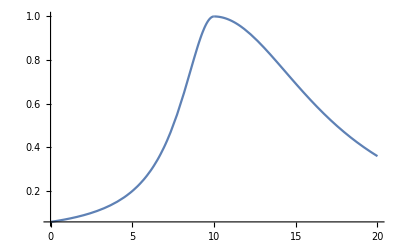

```mathematica
Plot[1/(1+(((x-10)/5)/(1/2 Sign[x-10]+1))^2),{x,0,20},PlotRange->All]
```

```mathematica
Sum[πMat[[α,λ]]πMat[[λ,γ]]gMN[[γ,β]]gMN[[2,μp]]gMN[[2,νp]]Δ4[[α,β,μp,νp]],{α,4},{β,4},{γ,4},{λ,4},{μp,4},{νp,4}]//FullSimplify
```

1/3 ((1+u1^2+u0^2 (-1+2 u1^2)) π00^2-2 u1 u2 π02 π10-2 u1^3 u2 π02 π10+2 u0 u1 π10 π11+2 u0 u1^3 π10 π11-2 π11^2-4 u1^2 π11^2-2 u1^4 π11^2-2 u1 u2 π11 π12-2 u1^3 u2 π11 π12+2 π02 π20-u0^2 π02 π20+2 u1^2 π02 π20+2 u0^2 u1^2 π02 π20+u2^2 π02 π20-2 u1^2 u2^2 π02 π20+2 u0 u1 π12 π20+2 u0 u1^3 π12 π20+u0 π00 (u2 π02-2 u1 (π01+u1^2 π01+u1 u2 π02)+2 u1 (1+u1^2) π10+(-1+2 u1^2) u2 π20)-π01 ((1+u0^2+3 u1^2-2 u0^2 u1^2+2 u1^4) π10+2 u0 (u1+u1^3) π11+u0 (-1+2 u1^2) u2 π12+2 (u1+u1^3) u2 π20)-2 u0 u1 π02 π21-2 u0 u1^3 π02 π21-u0 u2 π10 π21+2 u0 u1^2 u2 π10 π21-2 u1 u2 π11 π21-2 u1^3 u2 π11 π21-π12 π21-3 u1^2 π12 π21-2 u1^4 π12 π21+u2^2 π12 π21-2 u1^2 u2^2 π12 π21+u0 u2 π02 π22-2 u0 u1^2 u2 π02 π22-2 u1 u2 π12 π22-2 u1^3 u2 π12 π22-u0 u2 π20 π22+2 u0 u1^2 u2 π20 π22-2 u1 u2 π21 π22-2 u1^3 u2 π21 π22+π22^2+u1^2 π22^2+u2^2 π22^2-2 u1^2 u2^2 π22^2+2 π03 π30-u0^2 π03 π30+2 u1^2 π03 π30+2 u0^2 u1^2 π03 π30+2 u0 u1 π13 π30+2 u0 u1^3 π13 π30-u0 u2 π23 π30+2 u0 u1^2 u2 π23 π30-2 u0 u1 π03 π31-2 u0 u1^3 π03 π31-π13 π31-3 u1^2 π13 π31-2 u1^4 π13 π31-2 u1 u2 π23 π31-2 u1^3 u2 π23 π31+u0 u2 π03 π32-2 u0 u1^2 u2 π03 π32-2 u1 u2 π13 π32-2 u1^3 u2 π13 π32+2 π23 π32+2 u1^2 π23 π32+u2^2 π23 π32-2 u1^2 u2^2 π23 π32+(1+u1^2) π33^2)

```mathematica
4/3 e u0^2-e/3 g00+ℏc π00/.{e->35.71241781625078,u0->1.004526510491177,g00->1,π00->0.1267143353265179,ℏc->19733/100000}
```

36.1695

```mathematica
Tμν=({{T00,T01,T02,T03},{T10,T11,T12,T13},{T20,T21,T22,T23},{T30,T31,T32,T33}}//.({T10->T01,T20->T02,T21->T12,T00->Rationalize[#1,0],T11->Rationalize[#2,0],T22->Rationalize[#3,0],T33->Rationalize[#4,0],T01->-Rationalize[#5,0],T02->-Rationalize[#6,0],T03->-Rationalize[#7,0],T12->-Rationalize[#8,0],T23->-Rationalize[#9,0],T13->-Rationalize[#10,0],T31->T13,T32->T23,T10->T01,T20->T02,T30->T03,T21->T12}&[36.16947129254363,14.10763023400852,20.64141155995377,1.420429498581335,3.110011799235606,-3.584160899069362,-0.9189564638617905,-3.405043570206334,0.3818912151297781,7.116858192364345]));
Tμν.gMN//N//MatrixForm
Eigensystem[Tμν.gMN//N]//Transpose//MatrixForm
(normedus=(#/√Abs[(#[[1]])^2-(#[[2]])^2-(#[[3]])^2-(#[[4]])^2])&/@Eigenvectors[Tμν.gMN//N])//MatrixForm
(#[[1]])^2-(#[[2]])^2-(#[[3]])^2-(#[[4]])^2&[normedus[[1]]]
```

(36.1695 | 3.11001 | -3.58416 | -0.918956
-3.11001 | -14.1076 | -3.40504 | 7.11686
3.58416 | -3.40504 | -20.6414 | 0.381891
0.918956 | 7.11686 | 0.381891 | -1.42043)

(35.7124 | {-0.995534,0.0649063,-0.0673261,-0.0128898}
-22.638 | {-0.022318,-0.499247,-0.846477,0.183661}
-14.9058 | {0.0898809,-0.754664,0.529298,0.377157}
1.83144 | {-0.0190631,0.419279,-0.051169,0.906214})

(-1.00453 | 0.0654926 | -0.0679343 | -0.0130062
-0.0223292 | -0.499496 | -0.846899 | 0.183752
0.090616 | -0.760835 | 0.533627 | 0.380241
-0.01907 | 0.419431 | -0.0511876 | 0.906543)

1.

```mathematica
Tr[Tμν.gMN]//N
```

6.33476×10^-15

```mathematica
u={u0,u1,u2,u3}
```

{u0,u1,u2,u3}

```mathematica
(e u⊗u-Pneq(gMN-u⊗u)+{{π00,π01,π02,π03},{π10,π11,π12,π13},{π20,π21,π22,π23},{π30,π31,π32,π33}}).gMN//FullSimplify
```

{{e u0^2+Pneq (-1+u0^2)+π00,-(e+Pneq) u0 u1-π01,-(e+Pneq) u0 u2-π02,-(e+Pneq) u0 u3-π03},{(e+Pneq) u0 u1+π10,-e u1^2-Pneq (1+u1^2)-π11,-(e+Pneq) u1 u2-π12,-(e+Pneq) u1 u3-π13},{(e+Pneq) u0 u2+π20,-(e+Pneq) u1 u2-π21,-e u2^2-Pneq (1+u2^2)-π22,-(e+Pneq) u2 u3-π23},{(e+Pneq) u0 u3+π30,-(e+Pneq) u1 u3-π31,-(e+Pneq) u2 u3-π32,-e u3^2-Pneq (1+u3^2)-π33}}

```mathematica
%//MatrixForm
((%//Tr)/.u0->√(1+u1^2+u2^2+u3^2))//FullSimplify
```

(e u0^2+Pneq (-1+u0^2)+π00 | -(e+Pneq) u0 u1-π01 | -(e+Pneq) u0 u2-π02 | -(e+Pneq) u0 u3-π03
(e+Pneq) u0 u1+π10 | -e u1^2-Pneq (1+u1^2)-π11 | -(e+Pneq) u1 u2-π12 | -(e+Pneq) u1 u3-π13
(e+Pneq) u0 u2+π20 | -(e+Pneq) u1 u2-π21 | -e u2^2-Pneq (1+u2^2)-π22 | -(e+Pneq) u2 u3-π23
(e+Pneq) u0 u3+π30 | -(e+Pneq) u1 u3-π31 | -(e+Pneq) u2 u3-π32 | -e u3^2-Pneq (1+u3^2)-π33)

e-3 Pneq+π00-π11-π22-π33

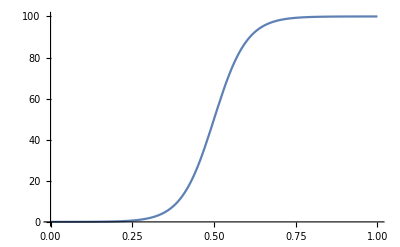

```mathematica
Plot[100(1/(Exp[-(e-es)/ξ]+1)-1/(Exp[es/ξ]+1))/.{es->0.5,ξ->0.05},{e,0,1}]
```

```mathematica
u={u0,u1,u2,u3}/.Rationalize[{u0->1.004526510491177,u1->-0.06549261154391076,u2->0.06793427954408042,u3-> 0.02167703441466333 τ0,τ0->0.6},0];
πμν=({{π00,π01,π02,π03},{π10,π11,π12,π13},{π20,π21,π22,π23},{π30,π31,π32,π33}}//.({π10->π01,π20->π02,π21->π12,π30->π03,π31->π13,π32->π23,π00->Rationalize[#1,0],π01->Rationalize[#2,0],π02->Rationalize[#3,0],π03->Rationalize[#4,0]τ0,π11->Rationalize[#5,0],π12->Rationalize[#6,0],π13->Rationalize[#7,0]τ0,π22->Rationalize[#8,0],π23->Rationalize[#9,0]τ0,π33->Rationalize[#10,0] τ0^2,τ0->3/5}&[0.1267143353265179, 0.1147179621702949, 1.696281332225715, 2.507189745022878, 10.13166165031851, 18.32947015718243,-59.76795606233844, 43.16449312764307,-3.580889866005392,-147.6928901184306]));
4/3 e u0^2-e/3 g00+ℏc π00/.{e->35.71241781625078,u0->1.004526510491177,g00->1,π00->0.1267143353265179,ℏc->19733/100000}
N[(4/3 e u⊗u-e/3 gMN+ℏc πμν)//.{e->Rationalize[35.71241781625078,0],ℏc->Rationalize[0.1973269718,0],τ0->3/5},10]//MatrixForm
```

36.1695

(36.16947129 | -3.110011799 | 3.584160899 | 0.9189564639
-3.110011799 | 14.10763023 | 3.40504357 | -7.116858192
3.584160899 | 3.40504357 | 20.64141156 | -0.3818912151
0.9189564639 | -7.116858192 | -0.3818912151 | 1.420429499)

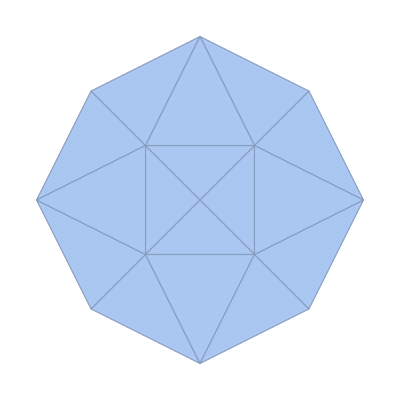

```mathematica
{{0,0},{1,0},{-1,0},{0,1},{0,-1},3^-1{1,1},2/3{1,1},3^-1{1,-1},2/3{1,-1},3^-1{-1,1},2/3{-1,1},3^-1{-1,-1},2/3{-1,-1}}//DelaunayMesh
```

```mathematica
gMP={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
gMN=-gMP;
u={u0,u1,u2,u3}/.Rationalize[{u0->1.00288,u1->-0.0035889,u2->0.0758759,u3-> 0 τ0,τ0->0.6},0];
πμν=({{π00,π01,π02,π03},{π10,π11,π12,π13},{π20,π21,π22,π23},{π30,π31,π32,π33}}//.({π10->π01,π20->π02,π21->π12,π30->π03,π31->π13,π32->π23,π00->Rationalize[#1,0],π01->Rationalize[#2,0],π02->Rationalize[#3,0],π03->Rationalize[#4,0]τ0,π11->Rationalize[#5,0],π12->Rationalize[#6,0],π13->Rationalize[#7,0]τ0,π22->Rationalize[#8,0],π23->Rationalize[#9,0]τ0,π33->Rationalize[#10,0] τ0^2,τ0->2/5}&[2.65541,-1.65641,35.0193,0,484.622,1.02907,0,462.912,0,-5905.49]));
N[(4/3 e u⊗u-e/3 gMN+ℏc πμν)//.{e->Rationalize[559.35,0],ℏc->Rationalize[0.1973269718,0],τ0->2/5},10]//MatrixForm
πμν[[1,1]]-πμν[[2,2]]-πμν[[3,3]]-πμν[[4,4]]//N
```

(564.175978 | -3.011164602 | 63.66147279 | 0
-3.011164602 | 282.0885978 | -0.00002628998873 | 0
63.66147279 | -0.00002628998873 | 282.0887073 | 0
0 | 0 | 0 | 6.608770873×10^-6)

-0.00019

```mathematica
u⊗u//MatrixForm//N
```

(1.00577 | -0.00359924 | 0.0760944 | 0.
-0.00359924 | 0.0000128802 | -0.000272311 | 0.
0.0760944 | -0.000272311 | 0.00575715 | 0.
0. | 0. | 0. | 0.)